```mathematica
parse[s_]:=ToExpression@StringReplace[s,"e"->"*^"]
```

```mathematica
readq[file_]:=Module[{rawdata,xlow,step,data,nx},
rawdata=StringSplit/@StringSplit[Import[file],"\n"];
xlow=parse@rawdata[[4,1]];
step=parse@rawdata[[5,1]];
data=Map[parse,rawdata[[7;;]],{2}];
nx=Length@data;
<|
x->(Range@nx-1/2)*step+xlow,
h->data[[All,1]],
hu->data[[All,2]],
hv->data[[All,3]]
|>
]
readbath[file_]:=Module[{rawdata,xlow,step,data,nx},
rawdata=StringSplit/@StringSplit[Import[file],"\n"];
data=Map[parse,rawdata[[7;;]],{2}];
nx=Length@data;
data[[All,-1]]
]
```

```mathematica
qRef=readq["\\\\Ubuntu\\claw_results\\_output\\fort.ref.q0001"];
bath=readbath["\\\\Ubuntu\\claw_results\\_output\\fort.a0000"];
```

```mathematica
bathLow=readbath["\\\\Ubuntu\\claw_results\\_output\\fort.low.a0000"];
qUnb1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qunb.q0001"];
qUnb2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qunb.q0002"];
qUnb5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qunb.q0005"];
qUnb10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qunb.q0010"];
```

```mathematica
qLev1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qlev.q0001"];
qLev2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qlev.q0002"];
qLev5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qlev.q0005"];
qLev10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qlev.q0010"];
```

-0.5

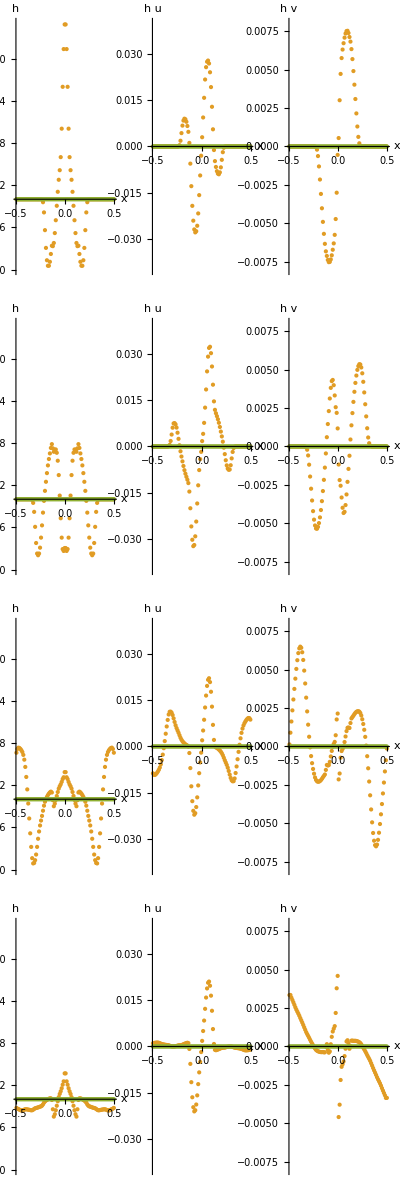

```mathematica
xlow=qRef[x][[1]]-(qRef[x][[2]]-qRef[x][[1]])/2
GraphicsGrid[#,ImageSize->1200]&/@List/@{
{
ListPlot[{Transpose[{qRef[x],1+0qRef[x]}],Transpose[{qUnb1[x],qUnb1[h]+bathLow}],Transpose[{qLev1[x],qLev1[h]+bathLow}]},AxesOrigin->{xlow,1},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h},PlotRange->{0.99,1.025}],
ListPlot[{Transpose[{qRef[x],0qRef[x]}],Transpose[{qUnb1[x],qUnb1[hu]}],Transpose[{qLev1[x],qLev1[hu]}]},AxesOrigin->{xlow,0},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h u},PlotRange->{-0.04,0.04}],
ListPlot[{Transpose[{qRef[x],0qRef[x]}],Transpose[{qUnb1[x],qUnb1[hv]}],Transpose[{qLev1[x],qLev1[hv]}]},AxesOrigin->{xlow,0},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h v},PlotRange->{-0.008,0.008}]
},
{
ListPlot[{Transpose[{qRef[x],1+0qRef[x]}],Transpose[{qUnb1[x],qUnb2[h]+bathLow}],Transpose[{qLev2[x],qLev2[h]+bathLow}]},AxesOrigin->{xlow,1},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h},PlotRange->{0.99,1.025}],
ListPlot[{Transpose[{qRef[x],0qRef[x]}],Transpose[{qUnb1[x],qUnb2[hu]}],Transpose[{qLev2[x],qLev2[hu]}]},AxesOrigin->{xlow,0},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h u},PlotRange->{-0.04,0.04}],
ListPlot[{Transpose[{qRef[x],0qRef[x]}],Transpose[{qUnb1[x],qUnb2[hv]}],Transpose[{qLev2[x],qLev2[hv]}]},AxesOrigin->{xlow,0},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h v},PlotRange->{-0.008,0.008}]
},
{
ListPlot[{Transpose[{qRef[x],1+0qRef[x]}],Transpose[{qUnb1[x],qUnb5[h]+bathLow}],Transpose[{qLev5[x],qLev5[h]+bathLow}]},AxesOrigin->{xlow,1},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h},PlotRange->{0.99,1.025}],
ListPlot[{Transpose[{qRef[x],0qRef[x]}],Transpose[{qUnb1[x],qUnb5[hu]}],Transpose[{qLev5[x],qLev5[hu]}]},AxesOrigin->{xlow,0},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h u},PlotRange->{-0.04,0.04}],
ListPlot[{Transpose[{qRef[x],0qRef[x]}],Transpose[{qUnb1[x],qUnb5[hv]}],Transpose[{qLev5[x],qLev5[hv]}]},AxesOrigin->{xlow,0},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h v},PlotRange->{-0.008,0.008}]
},
{
ListPlot[{Transpose[{qRef[x],1+0qRef[x]}],Transpose[{qUnb1[x],qUnb10[h]+bathLow}],Transpose[{qLev10[x],qLev10[h]+bathLow}]},AxesOrigin->{xlow,1},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h},PlotRange->{0.99,1.025}],
ListPlot[{Transpose[{qRef[x],0qRef[x]}],Transpose[{qUnb1[x],qUnb10[hu]}],Transpose[{qLev10[x],qLev10[hu]}]},AxesOrigin->{xlow,0},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h u},PlotRange->{-0.04,0.04}],
ListPlot[{Transpose[{qRef[x],0qRef[x]}],Transpose[{qUnb1[x],qUnb10[hv]}],Transpose[{qLev10[x],qLev10[hv]}]},AxesOrigin->{xlow,0},Joined->{True,False,False},PlotStyle->{Thin,PointSize@Medium,PointSize@Medium},AxesLabel->{x,h v},PlotRange->{-0.008,0.008}]
}
}//TableForm
```